```mathematica
testFileName = "/Users/dmsussma/repos/useCellGPU/imageTest/data/test.nc";
```

## Very basic visualization

```mathematica
(* This tells me the layout of the nc file I'm reading in...i.e., the names of the records in the nc file *)
Import[testFileName,"Datasets"]
```

{time,means0,pos,type,director,BoxMatrix}

```mathematica
(* Actually read the data in *)
{time,means0,pos,type,director,boxMatrix}=Import[testFileName,"Data"];
nFrames = Length[time]
```

31

```mathematica
(* For instance, apparently I save a snapshot of the system at the following times: *)
time
```

{{1.},{1.01},{1.02},{1.03},{1.04},{1.05},{1.06},{1.07},{1.08},{1.09},{1.1},{1.11},{1.13},{1.14},{1.16},{1.18},{1.2},{1.22},{1.25},{1.28},{1.32},{1.35},{1.4},{1.45},{1.5},{1.56},{1.63},{1.71},{1.79},{1.89},{2.}}

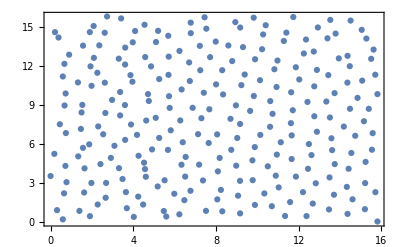

```mathematica
(* grab the cell centers in one of the frames *)
frame = 28;
positions=Partition[data[[3,frame]],2];
ListPlot[positions]
```

```mathematica
(* A function to start visualizing the monolayer by looking at the voronoi tesselation... *)
simpleCellFrame[pts_,cellColor_,faceColor_,vertexColor_,vertexSize_,edgeThickness_]:=Module[{min,vor,},
min=Min[pts]-.1;max=Max[pts]+.1;
vor=VoronoiMesh[pts,{{min,max},{min,max}}];
Show[
Graphics[{GraphicsComplex[MeshCoordinates[vor],
{
(* faces *)
cellColor,MeshCells[vor,2],
(*edges *)
faceColor,Thickness[edgeThickness],MeshCells[vor,1],
(* vertices*)
PointSize[vertexSize],vertexColor,MeshCells[vor,0]
}]}]
]
];
```

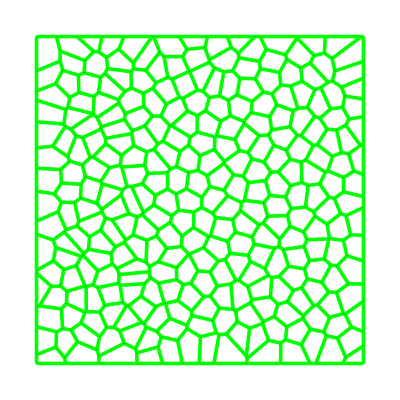

```mathematica
simpleCellFrame[positions,White,Green,Black,0.001,.0065]
```

```mathematica
(* An example with unnecessary, marginally fancier visual styling... *)
cellFrame[pts_,types_,cellColor1_,cellColor2_,edgeColor_,edgeThickness_,noiseLevel_]:=Module[{min,max,vor,nf,c,inds,indices,inside,outside,plates},
min=Min[pts]-.1;max=Max[pts]+.1;
vor=VoronoiMesh[pts,{{min,max},{min,max}}];
nf=Nearest[pts->Automatic];
c=PropertyValue[{vor,2},MeshCellCentroid];
inds=Join@@(nf/@c);
indices=Table[i,{i,1,Length[pts]}];
inside=Select[indices,types[[inds[[#]]]]==0&];
outside=Select[indices,types[[inds[[#]]]]==1&];

plot=ImageEffect[Show[
Graphics[{GraphicsComplex[MeshCoordinates[vor],

{
(* vertices*)
PointSize[0.00],Red,MeshCells[vor,0],
(* faces *)
Opacity[cellColor1[[1]]],cellColor1[[2]],MeshCells[vor,2][[inside]],
Opacity[cellColor2[[1]]],cellColor2[[2]],MeshCells[vor,2][[outside]],
(*edges *)
edgeColor,Thickness[edgeThickness],MeshCells[vor,1]
}]}]
],{"GaussianNoise",noiseLevel}];
Show[plot,Background->White]
];
```

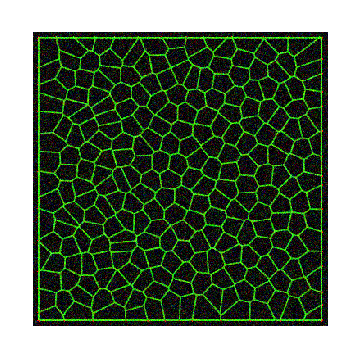

```mathematica
cellFrame[positions,type[[1]],{.825,Black},{.88,Black},RGBColor[66/256,235/256,17/256],.005,.15]
```